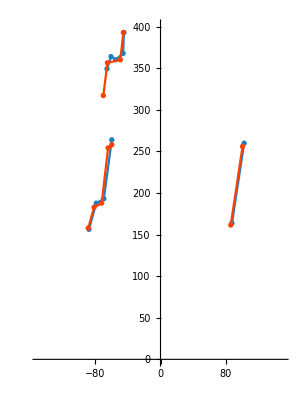

```mathematica
(* --- Frame 1523 --- *)
frameA = {{-87.553008, 156.3}, {-86.4554445, 163.}, {-85.1054589, 169.4}, {-83.63416365, 176.3}, {-81.2778156, 182.8}, {-78.5697921, 187.8}, {-71.9949141, 187.8}, {-69.29441775, 193.1}, {-69.6002301, 199.8}, {-68.8139055, 206.9}, {-67.208697, 213.3}, 
    {-67.07828475, 221.5}, {-64.8843831, 227.4}, {-64.5811965, 233.5}, {-64.69848, 240.}, {-62.6903064, 248.7}, {-61.841664, 256.}, {-59.59244655, 263.9}, {-65.42511255, 349.3}, {-63.6534315, 356.5}, {-60.53229, 364.}, {-54.8561187, 360.2}, 
    {-51.611742, 364.}, {-45.72463545, 367.9}, {-45.40289355, 375.9}, {-45.0603207, 384.2}, {-44.7165225, 393.}, {102.36486375, 259.9}, {101.13811335, 252.3}, {99.2747061, 243.4}, {98.19937395, 236.7}, {97.36753635, 228.9}, {96.158466, 221.5}, 
    {95.21232075, 213.3}, {88.5409902, 178.1}, {88.6551228, 171.1}, {87.4532295, 163.8}}; 

(* --- Frame 1526 --- *)
frameB = {{-88.393248, 157.8}, {-86.8797657, 163.8}, {-86.1032439, 170.2}, {-83.9427768, 176.3}, {-81.2778156, 182.8}, {-75.3737292, 184.8}, {-71.9949141, 187.8}, {-71.756496, 195.2}, {-71.10898605, 202.1}, {-69.6786525, 209.5}, {-68.500566, 217.4}, 
    {-68.0153274, 225.9}, {-67.033647, 233.5}, {-65.95884, 240.}, {-65.26196595, 246.9}, {-64.0767024, 254.2}, {-59.615028, 258.}, {-69.9625836, 317.2}, {-69.6635982, 326.2}, {-69.823944, 332.4}, {-68.836662, 339.}, {-67.7961648, 345.8}, 
    {-64.901538, 356.5}, {-61.1572185, 356.5}, {-55.4866488, 360.2}, {-49.1813478, 360.2}, {-47.7504891, 384.2}, {-45.404469, 393.}, {100.380672, 256.}, {98.82430245, 248.7}, {97.73514135, 241.7}, {96.3009567, 235.1}, {95.76477855, 228.9}, 
    {94.1772501, 218.7}, {93.6829089, 210.7}, {91.8161757, 203.3}, {91.4503212, 196.4}, {89.8944768, 188.8}, {88.9576092, 182.8}, {88.1198199, 175.4}, {87.0646185, 168.6}, {85.942548, 161.5}}; 

(* --- Colors --- *)
Black12 = RGBColor[0,0,0,0.125]; Black06 = RGBColor[0,0,0,0.0625]; Terra = RGBColor[1,0.25,0,1];Terra50 = RGBColor[1,0.25,0,0.5];Terra25 = RGBColor[1,0.25,0,0.25]; Terra12 = RGBColor[1,0.25,0,0.125]; BlueSky = RGBColor[0.125,0.5,0.75]; Olive = RGBColor[0.5,0.75,0.125];

(* --- ViewPrefs --- *)
aRatio = 4/3;
pRange = {{-150, 150},{0, 400}};
fSize = {300,400};

Row[{
Show[
ListPlot[{frameA[[1]], frameA[[6]], frameA[[8]], frameA[[18]], frameA[[19]], frameA[[21]],frameA[[22]], frameA[[24]], frameA[[27]], frameA[[28]], frameA[[-1]]}, AxesOrigin-> {0, 0}, AspectRatio-> aRatio, PlotRange-> pRange, ImageSize->fSize, PlotStyle->BlueSky],
ListLinePlot[{frameA[[1]], frameA[[6]], frameA[[8]], frameA[[18]]}, PlotStyle->BlueSky],
ListLinePlot[{frameA[[19]], frameA[[21]],frameA[[22]], frameA[[24]], frameA[[27]]}, PlotStyle->BlueSky],
ListLinePlot[{frameA[[28]], frameA[[-1]]}, AxesOrigin-> {0, 0}, AspectRatio-> aRatio, PlotRange-> pRange, ImageSize->fSize, PlotStyle->BlueSky],

ListPlot[{frameB[[1]],frameB[[5]],frameB[[7]],frameB[[16]],frameB[[17]],frameB[[18]],frameB[[23]],frameB[[26]],frameB[[28]],frameB[[29]],frameB[[-1]]},PlotStyle-> Terra],
ListLinePlot[{frameB[[1]],frameB[[5]],frameB[[7]],frameB[[16]],frameB[[17]]},PlotStyle-> Terra],
ListLinePlot[{frameB[[18]],frameB[[23]],frameB[[26]],frameB[[28]]},PlotStyle-> Terra],
ListLinePlot[{frameB[[29]],frameB[[-1]]},PlotStyle-> Terra]
]
}]
```